```mathematica
SetDirectory[NotebookDirectory[]];
γ=4;α=0.4;K=1.5;xmin=-50;xmax=50;maxtime=5;ep=0.08;filename="Fig2_pauwelussen.png";r1=1;r2=12;
```

{v→0.116905}

{v→1.2831}

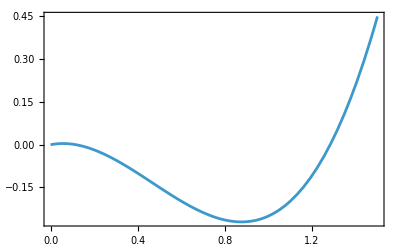

```mathematica
f[v_]=v(1-v)(v-α);
h[v_]=Min[f[-v],-f[v]];
a0=1;
(*h is positive for *)
eqn1=FindRoot[h[v]-v/γ==0,{v,0.2}]
eqn2=FindRoot[h[v]-v/γ==0,{v,1.3}]
a1=v/.eqn1;
b1=v/.eqn2;
Plot[{h[v]-v/γ},{v,0,1.5},PlotRange->All,Frame->True]
```

```mathematica
(*Copmuting parameters*)
I1=Integrate[h[v]-v/γ,{v,0,a1}];
I2=Integrate[h[v]-v/γ,{v,a1,b1}];
2/(r1)I2+(r2^3/r1^4)I1
```

0.193436

InterpolatingFunction[…]

InterpolatingFunction[…]

{x→-0.37869}

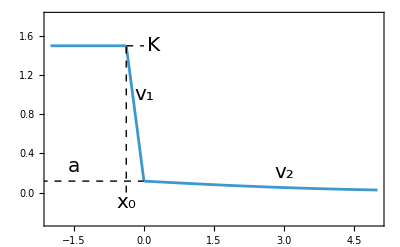

Fig2_pauwelussen.png

```mathematica
a=Min[1,a0,a1];
V2=NDSolveValue[{v''[x]==h[v[x]]-v[x]/γ,v[0]==a,v'[0]==-Sqrt[2]Sqrt[Integrate[h[u]-u/γ,{u,0,a}]]},v,{x,0,10}]

V1=NDSolveValue[{v''[x]==h[v[x]]-v[x]/γ,v[0]==a,v'[0]==-(r2^2/r1^2)Sqrt[2]Sqrt[Integrate[h[u]-u/γ,{u,0,a}]]},v,{x,-1,0}]

(*Together*)
eqnx0=FindRoot[V1[x]==K,{x,-1}]
x0=x/.eqnx0;
VV[x_]=Which[x<x0,K,x<0,V1[x],True,V2[x]];
g1=Plot[VV[x],{x,-2,5},Frame->True,PlotRange->{-0.3,1.8}];
lineK=Graphics[{Dashed,Line[{{x0,K},{0,K}}]}];
linex0=Graphics[{Dashed,Line[{{x0,0},{x0,K}}]}];
labelK=Graphics[Text[Style["K",FontSize->20],{0.2,K},{0,0}]];
labelx0=Graphics[Text[Style["x_0",FontSize->20],{x0,-0.1},{0,0}]];
linea=Graphics[{Dashed,Line[{{-10,a},{0,a}}]}];
labela=Graphics[Text[Style["a",FontSize->20],{-1.5,a+0.15},{0,0}]];
labelv1v2=Graphics[{Text[Style["v_1",FontSize->20],{0,1},{0,0}],
Text[Style["v_2",FontSize->20],{3,0.2},{0,0}]}];
img=Show[g1,lineK,labelK,linex0,labelx0,linea,labela,labelv1v2]
Export[filename,img]
```

```mathematica
{VV1,WW1}=NDSolveValue[{D[u[t, x], t] ==  D[u[t, x], x, x]+f[u[t, x]]+p1 g[u[t, x]]phi[x/0.3]- w[t,x], D[w[t, x], t] == ep (u[t, x] - γ w[t, x]), 
u[0, x] ==Which[Abs[x+3]<3,(1-Abs[x+3]/3)1.2,True,0], 
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot3D[VV1[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
Animate[Plot[{VV1[t,x],VV[x]},{x,-10,10},PlotRange->{{-10,10},{-2,2}}],{t,0,maxtime},AnimationRunning->False,AnimationRepetitions->1]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

```mathematica
x0
```

-0.37869